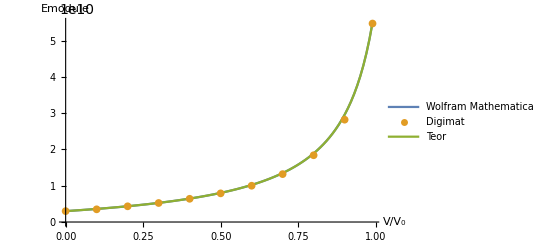

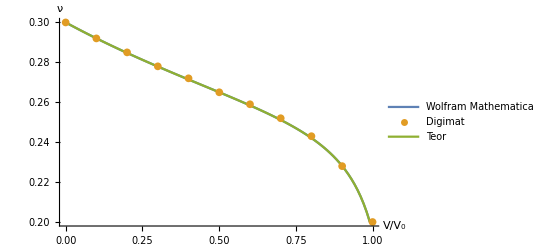

```mathematica
(*ДЛЯ СФЕРЫ*)
Fun2[x_]:=Module[{y={{C11,C12,C12,0,0,0},{C12,C11,C12,0,0,0},{C12,C12,C11,0,0,0},{0,0,0,(C11-C12)/2,0,0},{0,0,0,0,(C11-C12)/2,0},{0,0,0,0,0,(C11-C12)/2}}},
y=x;
y[[4]]=2*y[[4]];
y[[5]]=2*y[[5]];
y[[6]]=2*y[[6]];
Return[y];
];
Fun4[x_]:=Module[{y={{C11,C12,C12,0,0,0},{C12,C11,C12,0,0,0},{C12,C12,C11,0,0,0},{0,0,0,(C11-C12)/2,0,0},{0,0,0,0,(C11-C12)/2,0},{0,0,0,0,0,(C11-C12)/2}}},
y=x;
y[[4]]=4*y[[4]];
y[[5]]=4*y[[5]];
y[[6]]=4*y[[6]];
Return[y];
];
Fun05[x_]:=Module[{y={{C11,C12,C12,0,0,0},{C12,C11,C12,0,0,0},{C12,C12,C11,0,0,0},{0,0,0,(C11-C12)/2,0,0},{0,0,1,0,(C11-C12)/2,0},{0,0,0,0,0,(C11-C12)/2}}},
y=x;
y[[4]]=0.5*y[[4]];
y[[5]]=0.5*y[[5]];
y[[6]]=0.5*y[[6]];
Return[y];
];
vecE=vecv=vecK=vecmu=vecEt=vecvt={};
For[i=0,i≤100,i++,
Ee=3*10^9;
v=0.3;
Ee1=55*10^9;
v1=0.2;
a1=1;
a2=1;
a3=1;
c1=i/100;
c0=1-c1;
C11=(Ee(1-v))/((1+v)(1-2v));
C12=(Ee*v)/((1+v)(1-2v));
Cmatr={{C11,C12,C12,0,0,0},{C12,C11,C12,0,0,0},{C12,C12,C11,0,0,0},{0,0,0,(C11-C12)/2,0,0},{0,0,0,0,(C11-C12)/2,0},{0,0,0,0,0,(C11-C12)/2}};
K1=Ee/(3*(1-2*v));
mu1=Ee/(2*(1+v));
MatrixForm[Cmatr];

C11=(Ee1(1-v1))/((1+v1)(1-2v1));
C12=(Ee1*v1)/((1+v1)(1-2v1));
Cmatr2={{C11,C12,C12,0,0,0},{C12,C11,C12,0,0,0},{C12,C12,C11,0,0,0},{0,0,0,(C11-C12)/2,0,0},{0,0,0,0,(C11-C12)/2,0},{0,0,0,0,0,(C11-C12)/2}};
K2=Ee1/(3*(1-2*v1));
mu2=Ee1/(2*(1+v1));
MatrixForm[Cmatr2];
a1=1;
a2=1;
a3=1;
s11=s22=s33=(7-5v)/(15(1-v));
s12=s23=s31=s13=s21=s32=(5v-1)/(15(1-v));
s44=s55=s66=(4-5v)/(15(1-v));

S={{s11,s12,s13,0,0,0},{s21,s22,s23,0,0,0},{s31,s32,s33,0,0,0},{0,0,0,s44,0,0},{0,0,0,0,s55,0},{0,0,0,0,0,s66}};
MatrixForm[S];
T1=Inverse[Fun4[(Fun05[IdentityMatrix[6]]+(S.(Fun2[Inverse[Fun4[Cmatr]]]).(Fun2[Cmatr2-Cmatr])))]];

MatrixForm[T1];

eps=Inverse[Fun4[(c0*Fun05[IdentityMatrix[6]]+c1*T1)]];

A1=T1.Fun2[eps];
MatrixForm[A1];
A0=Inverse[Fun4[c0*Fun05[IdentityMatrix[6]]-c1*T1]];
MatrixForm[A0];
Ccomp=Cmatr+(c1*(Cmatr2-Cmatr)).Fun2[A1];
MatrixForm[Ccomp];
Enew=((Ccomp[[1]][[1]])^2+Ccomp[[1]][[1]]Ccomp[[1]][[2]]-2*(Ccomp[[1]][[2]])^2)/(Ccomp[[1]][[1]]+Ccomp[[1]][[2]]);
vnew=(Ccomp[[1]][[2]])/(Ccomp[[1]][[1]]+Ccomp[[1]][[2]]);
KTeor=K1+(c1*K1*(K2-K1)*(3*K1+4*mu1))/(3*(1-c1)*(K2-K1)*K1+K1*(3*K1+4*mu1));
muTeor=mu1+(5*c1*mu1*(mu2-mu1)*(3K1+4*mu1))/(6*(1-c1)(mu2-mu1)(K1+2mu1)+5*mu1*(3K1+4mu1));
(*KTeor=K1+(c1*(K2-K1)*(3*K1+4*mu1))/(3*K1+4*mu1);*)
(*muTeor=mu1+(15(mu2-mu1)(1-v)c1*mu1)/((7-5v)mu1+2(4-5v1)mu2);*)
Knew=Enew/(3*(1-2vnew));
munew=Enew/(2*(1+vnew));
vTeor=(3KTeor-2muTeor)/(6KTeor+2muTeor);
ETeor=2muTeor+2muTeor*(3KTeor-2muTeor)/(6KTeor+2muTeor);

AppendTo[vecE,Enew];
AppendTo[vecv,vnew];
AppendTo[vecEt,ETeor];
AppendTo[vecvt,vTeor];
AppendTo[vecK,Knew];
AppendTo[vecmu,munew];

];

x={};
dataE={};
datav={};
For[i=0,i<Length[vecE],i++,
AppendTo[x,i/Length[vecE]];
];
For[i=1,i<Length[vecE],i++,
AppendTo[dataE,{x[[i]],vecE[[i]]}];
AppendTo[datav,{x[[i]],vecv[[i]]}];
];
(*Апроксимируем графики изходя из полученных точек многочленом 5 степени*)
(*fitE=LinearModelFit[dataE,{y,y^2,y^3,y^4,y^5},y];
fitv=LinearModelFit[datav,{y,y^2,y^3,y^4,y^5},y];*)
DigimatDataE={{0,3*10^9},{0.1,3.5*10^9},{0.2,4.33*10^9},{0.3,5.24*10^9},{0.4,6.4*10^9},{0.5,7.9*10^9},{0.6,10*10^9},{0.7,13.2*10^9},{0.8,18.4*10^9},{0.9,28.2*10^9},{0.99,5.47*10^10}};
DigimatDatav={{0,0.3},{0.1,0.292},{0.2,0.285},{0.3,0.278},{0.4,0.272},{0.5,0.265},{0.6,0.259},{0.7,0.252},{0.8,0.243},{0.9,0.228},{0.999,0.2}};

(*Plot[fitE[y],{y,0,1}]*)
(*ListPlot[Table[{DigimatDataE[[i]][[1]],DigimatDataE[[i]][[2]]},{i,Length[DigimatDataE]}]]*)
(*Plot[fitv[y],{y,0,1}]*)
(*ListPlot[Table[{DigimatDatav[[i]][[1]],DigimatDatav[[i]][[2]]},{i,Length[DigimatDatav]}]]*)
ListPlot[{Table[{x[[i]],vecE[[i]]},{i,Length[x]}],Table[{DigimatDataE[[i]][[1]],DigimatDataE[[i]][[2]]},{i,Length[DigimatDataE]}],Table[{x[[i]],vecEt[[i]]},{i,Length[x]}]},Joined->{True,False,True},AxesLabel->{V/Subscript[V, 0],Emodule},PlotLegends->{"Wolfram Mathematica","Digimat","Teor"}]
ListPlot[{Table[{x[[i]],vecv[[i]]},{i,Length[x]}],Table[{DigimatDatav[[i]][[1]],DigimatDatav[[i]][[2]]},{i,Length[DigimatDatav]}],Table[{x[[i]],vecvt[[i]]},{i,Length[x]}]},Joined->{True,False,True},AxesLabel->{V/Subscript[V, 0],ν},PlotLegends->{"Wolfram Mathematica","Digimat","Teor"}]

(*ListPlot[Table[{x[[i]],vecK[[i]]},{i,Length[x]}]]*)
(*ListPlot[Table[{x[[i]],vecmu[[i]]},{i,Length[x]}]]*)
```